```mathematica
SetDirectory["C:\\Users\\pglpm\\repositories\\genobayes\\scripts2\\"];
```

```mathematica
bd[x_,a_,b_]=Assuming[0<x<1,FS@PDF[BetaDistribution[b,a],x]];
```

```mathematica
ClearAll[cd];cd[x_]=Assuming[Element[x,Reals],FS[PDF[CauchyDistribution[Log[1000],Log[1000]],x]]]
```

Log[1000]/(π (x^2-6 x Log[10]+18 Log[10]^2))

```mathematica
ClearAll[gd];gd[x_]=Assuming[x>0,FS[PDF[GammaDistribution[1,1000],x]]]
```

ⅇ^(-x/1000)/1000

```mathematica
priora[x_,a_]:=NIntegrate[bd[x,a*q,a*(1-q)],{q,0,1},AccuracyGoal->+Infinity,PrecisionGoal->3,MaxRecursion->10^6];
```

```mathematica
prior[x_]:=NIntegrate[bd[x,a*q,a*(1-q)]*cd[a],{a,0,+Infinity},{q,0,1},AccuracyGoal->+Infinity,PrecisionGoal->3,MaxRecursion->10^6];
```

```mathematica
prior[0.5]
```

0.993171

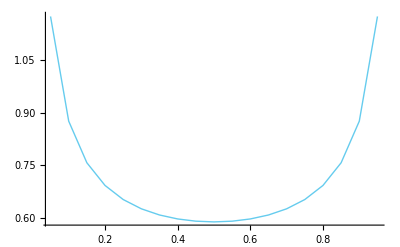

```mathematica
ListPlot[Table[{ii,priora[ii,2]},{ii,0.05,0.95,0.05}],Joined->True,PlotRange->All]
```

```mathematica
jpriora[x_,y_,a_]:=NIntegrate[bd[x,a*q,a*(1-q)]*bd[y,a*q,a*(1-q)],{q,0,1},AccuracyGoal->+Infinity,PrecisionGoal->3,MaxRecursion->10^6];
```

```mathematica
jprior[x_,y_]:=NIntegrate[bd[x,a*q,a*(1-q)]*bd[y,a*q,a*(1-q)]*gd[a],{a,0,+Infinity},{q,0,1},AccuracyGoal->+Infinity,PrecisionGoal->3,MaxRecursion->10^6];
```

```mathematica
ListPlot3D[Flatten[Table[{ii,jj,jpriora[ii,jj,10]},{ii,0.05,0.95,0.05},{jj,0.05,0.95,0.05}],1],PlotRange->Auto]
```

-Graphics3D-

```mathematica
Plot3D[jpriora[ii,jj,1],{ii,0.05,0.95},{jj,0.05,0.95},PlotRange->Auto]
```

$Aborted

```mathematica
jpriora[0.1,0.1,1]
```

0.764592

```mathematica
ListPlot3D[Flatten[Table[{ii,jj,jprior[ii,jj]},{ii,0.05,0.95,0.05},{jj,0.05,0.95,0.05}],1],PlotRange->All]
```

-Graphics3D-

```mathematica
Cuhre[x^2*y^2,{x,0,1},{y,0,1}]
```

{{0.111111,1.47347×10^-15,0.00114001}}

```mathematica
ils[y_]=Assuming[0<y<1,FS[x/.Solve[LogisticSigmoid[x]==y,x,Reals][[1]]]]
```

Log[-y/(-1+y)]

```mathematica
Assuming[a>0&&0<q<1&&0<x<1&&0<y<1,FS[bd[x,a*q,a*(1-q)]*bd[y,a*q,a*(1-q)]*gd[a]]]
```

(ⅇ^(-a/1000) ((-1+x) (-1+y))^(-1+a q) (x y)^(-1+a-a q))/(1000 Beta[a-a q,a q]^2)

```mathematica
%687/. {x->0.4,y->0.3, a->97.954803160145,q->0.5}
```

1.84793×10^-6

```mathematica
mina=10^-6;maxa=10^6;const=Integrate[gd[a],{a,mina,maxa}];jpriorc[x_,y_]:=NIntegrate[bd[x,a*q,a*(1-q)]*bd[y,a*q,a*(1-q)]*gd[a]
,{a,mina,maxa},{q,0,1},AccuracyGoal->+Infinity,PrecisionGoal->2,MaxPoints->10^6]/const;
```

```mathematica
jpriorc[0.4,0.3]
```

0.396606

```mathematica
ListPlot3D[Flatten[Table[{ii,jj,jpriorc[ii,jj]},{ii,0.05,0.95,0.05},{jj,0.05,0.95,0.05}],1],PlotRange->All,ViewPoint->Dynamic[viewpoint]]
```

-Graphics3D-

```mathematica
Install["C:\\Users\\pglpm\\work\\Cuba\\Cuhre.exe"];
```

```mathematica
mina=10^-6;maxa=5*10^2;const=Integrate[gd[a],{a,mina,maxa}];jpriorc[x_,y_]:=Cuhre[bd[x,a*q,a*(1-q)]*bd[y,a*q,a*(1-q)]*gd[a]
,{a,mina,maxa},{q,0,1},AccuracyGoal->+Infinity,PrecisionGoal->2,MaxPoints->10^6]/const;
```

```mathematica
jpriorc[0.4,0.3]
```

{{0.99844,0.00798428,6.59748×10^-21}}

```mathematica
ListPlot3D[Flatten[Table[{ii,jj,jpriorc[ii,jj][[1,1]]},{ii,0.05,0.95,0.05},{jj,0.05,0.95,0.05}],1],PlotRange->All,ViewPoint->Dynamic[viewpoint]]
```

-Graphics3D-

```mathematica
plot=ListPlot3D[Flatten[Table[{ii,jj,jpriora[ii,jj,30]},{ii,0.05,0.95,0.05},{jj,0.05,0.95,0.05}],1],PlotRange->Auto,ViewPoint->Dynamic[viewpoint],Ticks->{Auto,Auto,None},AxesLabel->{"freq"["symptom | 1st allele"],"frequency"["symptom | 2nd allele"],"prob. density"}]
```

-Graphics3D-

```mathematica
Show[plot]
```

-Graphics3D-

```mathematica
Export["test3df.pdf",plot,"AllowRasterization"->True,ImageSize->a5rsize*2];
```

```mathematica
Export["test3df.png",plot,ImageSize->a5rsize*2];
```

```mathematica
data=Import["dataset1_binarized.csv"][[2;;,2;;]];
```

```mathematica
allcouples=Flatten[Table[{ii,jj},{ii,93},{jj,ii+1,94}],1];
```

```mathematica
geneseq=Import["dataset1_binarized.csv"][[1,5;;]];
```

```mathematica
rsnp=RandomInteger[94]
```

84

```mathematica
symptoms={{1},{2}};snps={3+{rsnp}};
symptomvariants={{0},{1}};snpvariants={{0},{1}};
namesymptomvariants={"n","y"};
namesymptoms={"A","B","C"};
namesnps=Import["dataset1_binarized.csv"][[1,5;;]][[rsnp]];namesnpvariants={"0","1"};
numsymptoms=Length[symptoms];numsymptomvariants=Length[symptomvariants];numsnps=Length[snps];numsnpvariants=Length[snpvariants];namestatistics=Flatten@Table[ii<>jj,{ii,{"EV_","SD_","post.theta_","opt.theta_","max.spread_"}},{jj,namesymptomvariants}];
```

```mathematica
ClearAll[logpriortheta];logpriortheta[t_]:=cd[Total@t]-Log[Total@t];
```

```mathematica
<<conditional_freqs_1.m
```

```mathematica
spread=defaultspread;
```

```mathematica
condfreqstatistics[data,symptoms,symptomvariants,snps,snpvariants,namesymptoms,namesymptomvariants,namesnps,namesnpvariants,savedir,filename,logpriortheta,spread]//MF
```

((0.722309 | 0.726606
0.277691 | 0.273394
0.00807471 | 0.00815189
0.00807471 | 0.00815189
2221.33 | 2171.33
853.99 | 816.99
12.3292 | Null
4.98952 | Null
0.264813 | Null
0.264813 | Null)
(0.589542 | 0.578935
0.410458 | 0.421065
0.0088675 | 0.00902872
0.0088675 | 0.00902872
1813.66 | 1730.66
1262.72 | 1258.72
10.6573 | Null
7.7243 | Null
0.592722 | Null
0.592722 | Null))

```mathematica
sdata=data[[;;,Join[symptoms[[1]],snps[[1]]]]];
```

```mathematica
f=Table[Total[Boole/@Table[z==Join[symptomvariant,snpvariant],{z,sdata}]],{symptomvariant,symptomvariants},{snpvariant,snpvariants}]
```

{{1455,1868,503,542},{516,698,224,223}}

```mathematica
logprob[t_]:=Block[{r2=f+t},Total@Flatten@LogGamma[r2]-Total@LogGamma[Total@r2]+numsnpvariants*(LogGamma[Total@t]-Total@LogGamma[t])+Total[logpriortheta[t]]];
```

```mathematica
logprob[{1,2}]//N
```

-3569.87

```mathematica
thetas=Array[t,numsymptomvariants]
```

{t[1],t[2]}

```mathematica
thetas=Table[Unique["t"],numsymptomvariants]
```

{t45,t46}

```mathematica
FindArgMax[{logprob[thetas],Sequence@@((#>0)&/@thetas)},T[{thetas,Mean@T@f}]]
```

{41.0502,16.3425}

```mathematica
FindMaximum[{logprob[thetas],Sequence@@((#>0)&/@thetas)},T[{thetas,Mean@T@f}]]
```

{-3565.28,{t45→41.0502,t46→16.3425}}

```mathematica
test[[2]]
```

{t45→41.0502,t46→16.3425}

```mathematica
theta=thetas/.FindMaximum[{logprob[thetas],Sequence@@((#>0)&/@thetas)},T[{thetas,Mean@T@f}]][[2]]
```

{{t39,t40}/.{t39,1092},{t39,t40}/.{t40,1661/4}}

```mathematica
fnew=f+theta
```

{{1496.05,1909.05,544.05,583.05},{532.343,714.343,240.343,239.343}}

```mathematica
nnew=Total[fnew]
```

{2028.39,2623.39,784.393,822.393}

```mathematica
Sequence@@T[T[fnew]/nnew]
```

Sequence[{0.737555,0.727703,0.693594,0.708968},{0.262445,0.272297,0.306406,0.291032}]

```mathematica
Sqrt[(Times@@fnew)/(nnew^2*(1+nnew))]
```

{0.00976638,0.00868929,0.0164497,0.01583}

```mathematica
Sqrt@T[((nnew-T@fnew)*T@fnew)/(nnew^2*(1+nnew))]
```

{{0.00976638,0.00868929,0.0164497,0.01583},{0.00976638,0.00868929,0.0164497,0.01583}}

```mathematica
Table[Null,numsnpvariants-1,numsymptomvariants]
```

{{Null,Null},{Null,Null},{Null,Null}}

```mathematica
T@Join[{theta},Table[Null,numsnpvariants-1,numsymptomvariants]]
```

{{41.0502,Null,Null,Null},{16.3425,Null,Null,Null}}

```mathematica
quantities={(*EV*)Sequence@@T[T[fnew]/nnew],(*STD*)Sequence@@Sqrt[T[((nnew-T@fnew)*T@fnew)/(nnew^2*(1+nnew))]],(*(*Quantiles*)Sequence@@(T@Table[Quantile[BetaDistribution[Sequence@@(Reverse[fnew[[;;,al]]])],quantiles],{al,binoutcomes+1}]),*)(*f+theta*)Sequence@@fnew,(*posterior theta*)Sequence@@T[Join[{theta},Table[Null,numsnpvariants-1,numsymptomvariants]]]}
```

{{0.737555,0.727703,0.693594,0.708968},{0.262445,0.272297,0.306406,0.291032},{0.00976638,0.00868929,0.0164497,0.01583},{0.00976638,0.00868929,0.0164497,0.01583},{1496.05,1909.05,544.05,583.05},{532.343,714.343,240.343,239.343},{41.0502,Null,Null,Null},{16.3425,Null,Null,Null}}

```mathematica
spread[q_]:=Max/@Abs@ArrayReshape[Table[(q[[co,x]]-q[[co,y]])/(q[[co+numsymptomvariants,x]]+q[[co+numsymptomvariants,y]]),{co,numsymptomvariants},{x,numsnpvariants-1},{y,x+1,numsnpvariants}],{numsymptomvariants,Binomial[numsnpvariants,2]}]
```

```mathematica
spread[quantities]
```

{1.67685,1.67685}

```mathematica
Join[quantities,T[Join[{spread[quantities]},Table[Null,numsnpvariants-1,numsymptomvariants]]]]
```

{{0.737555,0.727703,0.693594,0.708968},{0.262445,0.272297,0.306406,0.291032},{0.00976638,0.00868929,0.0164497,0.01583},{0.00976638,0.00868929,0.0164497,0.01583},{1496.05,1909.05,544.05,583.05},{532.343,714.343,240.343,239.343},{41.0502,Null,Null,Null},{16.3425,Null,Null,Null},{1.67685,Null,Null,Null},{1.67685,Null,Null,Null}}